```mathematica
S[u_,v_,R_] := {R Sin[u]Cos[v], R Cos[u]Cos[v], R Sin[v]};
T[u_,v_,R_,r_] := {Cos[u](R+r Cos[v]), Sin[u](R+r Cos[v]), r Sin[v]}
```

```mathematica
(*Exercício 1.1*)
ParametricPlot3D[S[u,v,3], {u,0,2π},{v,-π/2, π/2}]
ParametricPlot3D[T[u,v,3,1],{u,0,2π},{v,0,2π}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Exercício 1.2*)
ParametricPlot3D[S[u,v,-1], {u,0,2π},{v,-π/2, π/2}]
(*Resultado: uma esfera de raio 1. Conclusão: Parâmetro R negativo resulta numa esfera de raio |R|, como pode também ser visto analiticamente*)
```

-Graphics3D-

```mathematica
(*Exercício 1.3*)
ParametricPlot3D[T[u,v,3,0],{u,0,2π},{v,0,2π}]
(*0=r<R resulta num aro circular*)

ParametricPlot3D[T[u,v,2,3],{u,0,4},{v,0,2π}]
(*0<R<r resulta num toro gordo, com autointerseções onde deveria estar um buraco*)
(*nota: o parâmetro u foi feito variar apenas entre 0 e 4<2π para poder ver estrutura interna*)

ParametricPlot3D[T[u,v,0,1],{u,0,2π},{v,0,2π}]
(*0=R<r resulta numa esfera*)
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*Exercício 1.4*)
plotTorus[R_] := ParametricPlot3D[T[u,v,R,1],{u,0,2π},{v,0,2π}]
ListAnimate[Table[plotTorus[R],{R,2,0,-.1}]]
(*O ListAnimate recebe uma lista de expressões e representa-as em sequência, formando uma animação.
A este, é dada uma lista, feita usando o Table, da forma
{plotTorus[2], plotTorus[1.9], plotTorus[1.8], ..., plotTorus[0]}
ou seja, é animado um toro com r=1 e R a variar em passos de .1 entre 2 e 0.*)

Animate[plotTorus[R],{R,2,0,-.1}]
(*O comando Animate é semânticamente equivalente ao ListAnimate daquela tabela, mas enquanto que no primeiro exemplo a tabela é pré-calculada, o animate calcula as coisas "on the fly", o que resulta neste ter de fazer gráficos mais "rough" para poder acompanhar o ritmo da animação.*)
```

```mathematica
(*Exercício 1.5*)
(*Vermelho: Curvas com u constante*)
(*Azul: Curvas com v constante*)
Show[
ParametricPlot3D[S[u,v,3], {u,0,2π},{v,-π/2, π/2}],
Table[
ParametricPlot3D[S[u,v,3], {v,-π/2, π/2}, PlotStyle->Directive[Red,Thickness[.02]] ],
{u,1,6}],
Table[
ParametricPlot3D[S[u,v,3], {u,0,2π},PlotStyle->Directive[Blue,Thickness[.02]]],
{v,-1,1,.5}]
]
Show[
ParametricPlot3D[T[u,v,3,1], {u,0,2π},{v,0,2π}],
Table[
ParametricPlot3D[T[u,v,3,1], {v,0,2π}, PlotStyle->Directive[Red,Thickness[.02]] ],
{u,1,6}],
Table[
ParametricPlot3D[T[u,v,3,1], {u,0,2π},PlotStyle->Directive[Blue,Thickness[.02]]],
{v,1,6}]
]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Exercício 1.6*)
(*O toro + a curva em questão*)
Show[
ParametricPlot3D[T[u,v,3,1], {u,0,2π},{v,0,2π}],
ParametricPlot3D[T[u,u,3,1], {u,0,2π},PlotStyle->Directive[Red,Thickness[.02]]]
]
(*Só a curva*)
(*Rodando a visualização, é claro que esta curva não forma um círculo no espaço*)
ParametricPlot3D[T[u,u,3,1], {u,0,2π},PlotStyle->Directive[Red,Thickness[.02]]]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Exercício 2.1 e 2.2*)
op[k_,n_] := Sum[d^k, {d, IntegerDigits[n]}]
op[5,68492]
op[5,2681]
op[5,73921]
AllTrue[Table[op[2,n], {n,1,10^5}], #<500&]
```

100649

40577

76132

True

```mathematica
(*Exercício 2.3*)
(*Sejam d0,...,dp os dígitos de n, ou seja,
n = d0 + 10d1 + ... + 10^p dp
Então, op(2,n) = d0^2 + d1^2 + ... + dp^2
≤ (d0^2 + d1^2) + (10d2 + 10d3 + ... + 10dp)
≤ (2*9^2) + (.1 d0 + d1 + 10d2 + 100d3 + ... + 10^(p-1) dp)
≤ 2*9^2 + n/10
Conclusão: op(2,n) ≤ 2*9^2 + n/10.
Consequentemente, se n>180=2*2*9*5 temos 2*9*9 < 9n/10, donde
op(2,n) ≤ 2*9^2 + n/10 < 9n/10 + n/10 = n,
i.e. op(2,n) < n.
Logo, a(i) não pode ser superior a 180 indefinidamente, pois sempre que a(i) é superior a 180, a(i+1) ≤ a(i) - 1. Logo, se a(i) fosse sempre superior a 180, tinhamos por exemplo, com n=a(0),
a(n) ≤ a(n-1) -1 ≤ a(n-2) -2 ≤ ... ≤ a(0) - n = 0, que é uma contradição porque a(n) é sempre positivo.
Isto mostra que para algum i≤n se tem a(i) ≤ 180. Vamos agora mostrar que temos também a(j) ≤ 180, para j≥i. Para este efeito basta mostrar: Se a(j) ≤ 180, então a(j+1) ≤ 180. Mas podemos reutilizar a desigualdade anterior e obtemos
a(j+1) = op(2,a(j)) ≤ 2*9^2 + a(j)/10 ≤ 162 + 18 = 180. Logo, por indução, temos a(j) ≤ 180 para todo o j≥i.
Concluindo, podemos considerar N = a(0), pois para algum i≤a(0) temos a(i)≤180, e consequentemente esta desigualdade aplica-se para todo o a(j) com j≥i, e em particular todo o j≥a(0). A demonstração é dada por terminada.*)
```

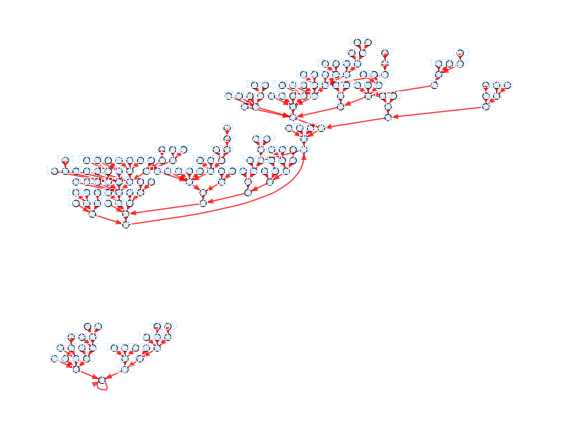

```mathematica
(*Exercício 2.4*)
Graph[Range[180],Table[k->op[2,k],{k,1,180}],VertexLabels->Placed["Name",Center],VertexSize->.6,VertexStyle->LightBlue,EdgeStyle->Directive[Red,Arrowheads[.02]],GraphLayout->"LayeredDigraphEmbedding"]
(*Este código produz um grafo cujos vértices são os números de 1 a 180 (Range[180]) e cujas arestas vão de cada k para op[2,k].*)
(*Temos também várias opções estilísticas:
VertexLabels -> Placed["Name,Center] coloca o nome de cada vértice no seu centro
VertexSize -> .6 faz com que cada vértice (circular) tenha um raio de .6 unidades
VertexStyle->LightBlue dá uma cor azul-claro a cada vértice
EdgeStyle->Directive[Red,Arrowheads[.02]] define o estilo de cada aresta. O comando Directive é usado para dar mais do que uma instrução gráfica, a primeira das quais faz com que cada aresta seja vermelha e a segunda mete o tamanho das pontas das setas a .02 unidades.
Finalmente, GraphLayout->"LayeredDigraphEmbedding" é usado para organizar os vértices em linhas para permitir melhor visualização do gráfo.*)

(*Através de observação do grafo é possível concluir que, de entre os valores menores ou iguais que 180, existem apenas dois ciclos nos quais as sucessões podem entrar: ou uma sucessão a(n) eventualmente é 1 e fica lá para sempre, ou entra no ciclo: 37, 58, 89, 145, 42, 20, 4, 16, 37,...
Como já vimos que todas as sucessões eventualmente tomam valores menores ou iguais que 180, concluimos que todas as sucessões entram num destes dois ciclos.*)
```

```mathematica
(*Exercício 2.5*)
reduce2[n_] := NestWhile[op[2,#]&, n, #≠1 && #≠4&]
(*Executa operações em n até chegar a 1 ou 4. Isto funciona porque sabemos que os únicos ciclos têm um destes números.*)
(*retorna 1 ou 4*)
Total[Table[If[reduce2[n]==1, 1, 0], {n,1,1000}]]/10//N
(*Resultado: 14.3%*)
```

```mathematica
(*Exercício 3.1*)
truncations[n_] := NestWhileList[Floor[#/10]&,n,#>10&]
righttruncatableQ[n_]:=AllTrue[truncations[n], PrimeQ]
Map[righttruncatableQ,{1997,1933,2333,71119,17133719,29399999}]
(*Apenas 71119 e 29399999 são truncáveis à direita.*)
```

{False,False,True,False,False,True}

```mathematica
(*Exercício 3.2*)
Select[Range[500], righttruncatableQ]
```

{2,3,5,7,23,29,31,37,53,59,71,73,79,233,239,293,311,313,317,373,379}

```mathematica
(*Exercício 3.3*)
(*Primeira tentativa: demora muito tempo*)
(*Select[Range[73939133], righttruncatableQ]*)
(*Segunda tentativa: Usar apenas os números primos*)
pi= PrimePi[73939133];
righttruncatables=Select[Map[Prime,Range[pi]], righttruncatableQ]
```

{2,3,5,7,23,29,31,37,53,59,71,73,79,233,239,293,311,313,317,373,379,593,599,719,733,739,797,2333,2339,2393,2399,2939,3119,3137,3733,3739,3793,3797,5939,7193,7331,7333,7393,23333,23339,23399,23993,29399,31193,31379,37337,37339,37397,59393,59399,71933,73331,73939,233993,239933,293999,373379,373393,593933,593993,719333,739391,739393,739397,739399,2339933,2399333,2939999,3733799,5939333,7393913,7393931,7393933,23399339,29399999,37337999,59393339,73939133}

```mathematica
(*Exercício 3.4*)
(*Sabemos que se houver um primo truncável com N dígitos, existem primos truncáveis com N-1, N-2, ... dígitos. Em contrapartida, se não houver primos truncáveis com N dígitos, não podem haver primos truncáveis com mais de N dígitos. Consequentemente, basta justificar que não há primos truncáveis com mais de 8 dígitos, basta mostrar que não há primos truncáveis com 9 dígitos.*)
(*Para fazer isso, usamos o seguinte processo. Começamos por reunir os primos truncáveis com 7 dígitos.*)
pt7 = {2339933,2399333,2939999,3733799,5939333,7393913,7393931,7393933}
(*Agora obtemos todos os com 8 dígitos a partir destes*)
(*Podemos fazer isto pois um primo truncável com 8 dígitos, quando removido o seu dígito das unidades, é um destes. Para mais, o seu dígito das unidades pode apenas ser 1, 3, 7 ou 9.*)
pt8 = Select[
Flatten[Table[10p7 + d, {p7, pt7}, {d,{1,3,7,9}}]]
,righttruncatableQ]
(*Repetimos o processo com os primos truncáveis com 8 dígitos, e como obtemos uma lista vazia concluímos que não há primos truncáveis com 9 dígitos, e o exercício fica concluído.*)
pt9 = Select[
Flatten[Table[10p8 + d, {p8, pt8}, {d,{1,3,7,9}}]]
,righttruncatableQ]
```

{2339933,2399333,2939999,3733799,5939333,7393913,7393931,7393933}

{23399339,29399999,37337999,59393339,73939133}

{}

```mathematica
(*Exercício 3.5*)
lefttruncations[n_] := NestWhileList[FromDigits[IntegerDigits[#][[2;;]]]&,n,#>10&]
lefttruncatableQ[n_]:=AllTrue[lefttruncations[n], PrimeQ]

(*alinea a) *)
Select[righttruncatables, lefttruncatableQ]
(*alinea b) *)
(*Vemos que 797 é duplamente truncável, mas não à esquerda e direita, pois 9 não é primo.*)
(*alinea c) *)
(*Reparamos primeiro que todos os primos de dois dígitos são truncáveis à direita e à esquerda, e o Mathematica calcula 25 destes.*)
PrimePi[100]
(*alinea d) *)
Total[Table[If[lefttruncatableQ[n],1,0],{n,1,1500}]]
lefttruncatableQ[357686312646216567629137]
```

{2,3,5,7,23,37,53,73,313,317,373,797,3137,3797,739397}

25

68

True